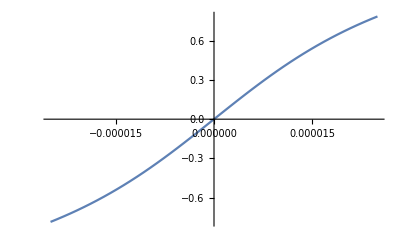

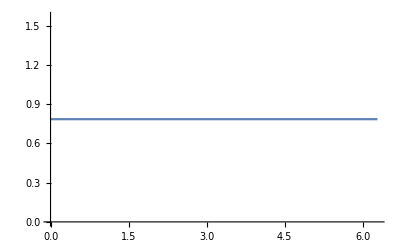

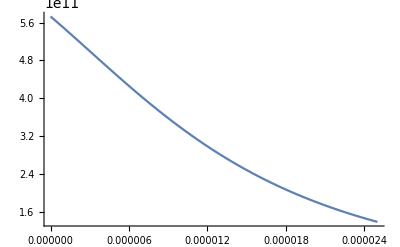

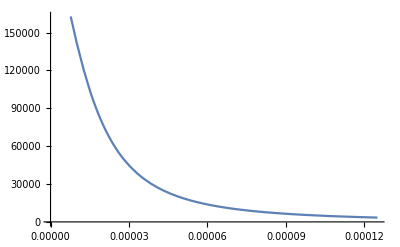

8.84737274132682×10^54319

```mathematica
gamma=40000;
eps1=1;
eps2=11.9;
eps3=250;
c=299792458;
hbar=1.05457173*^-34;
beta=Sqrt[1-1/gamma^2];
e=1.602*^-19;
n=2*^10;(*number of electrons*)
q=n*e;(*bunch charge in Coulombs*)
rad=0.02 ;(*lense diameter in m*)
d=0.05 ;(*distance from foil to lens in m*)
a=0.00010000000; (*size of diffraction slit in m*)
lowerlambda=300*^-9;(*Visible Spectrum m*)
averagelambda=500*^-9;
upperlambda=700*^-9;
eps0=8.854*^-12;
sigx=20*^-6;
sigy=sigx;
sigz=20*^-6;
alpha=7.297*^-3;

thetalens=ArcTan[a/(2*d)];
thetamax=1/gamma;

k[lambda_]:=
2*Pi/lambda
kx[lambda_,theta_,phi_]:=
k[lambda]*Sin[theta]*Cos[phi]
ky[lambda_,theta_,phi_]:=
k[lambda]*Sin[theta]*Sin[phi]
Eta[lambda_]:=
k[lambda]/(beta*gamma)
f[lambda_,theta_,phi_]:=
Sqrt[kx[lambda,theta,phi]^2+Eta[lambda]^2]

Ex[y_,lambda_,theta_,phi_]:=
I*e*kx[lambda,theta,phi]/(4*Pi^2*c*f[lambda,theta,phi])*(Exp[-(a/2-y)*(f[lambda,theta,phi]-I*ky[lambda,theta,phi])]/(f[lambda,theta,phi]-I*ky[lambda,theta,phi])+Exp[-(a/2+y)*(f[lambda,theta,phi]+I*ky[lambda,theta,phi])]/(f[lambda,theta,phi]+I*ky[lambda,theta,phi]))

Ey[y_,lambda_,theta_,phi_]:=
e/(4*Pi^2*c)*(Exp[-(a/2-y)*(f[lambda,theta,phi]-I*ky[lambda,theta,phi])]/(f[lambda,theta,phi]-I*ky[lambda,theta,phi])-Exp[-(a/2+y)*(f[lambda,theta,phi]+I*ky[lambda,theta,phi])]/(f[lambda,theta,phi]+I*ky[lambda,theta,phi]))

Dens[y_,y0_]:=
1/(Sqrt[2*Pi]*sigy)*Exp[-(y-y0)^2/(2*sigy^2)]

Nsingle2[y_,lambda_,theta_,phi_]:=
Pi^2*k[lambda]^2*c/(hbar*4*Pi*eps0) *1/lambda*(Abs[Ex[y,lambda,theta,phi]]^2+Abs[Ey[y,lambda,theta,phi]]^2)

Convolution[lambda_,theta_,phi_,y0_]:=
NIntegrate[Nsingle2[y,lambda,theta,phi]*Dens[y,y0],{y,-1*sigy,1*sigy}]

Nbunch2[lambda_,theta_,a_]:=
alpha/(4*Pi^2*lambda)*Exp[-2*Pi*a/(gamma*lambda)]/(theta^2+1/gamma^2)*(Exp[8*Pi^2*sigy^2/(gamma^2*lambda^2)-Cos[2*Pi*a/lambda*theta+2*Phi[lambda,theta,Pi/2]]])


(*NIntegrate[1/(Sqrt[2*Pi]*sigy)*Exp[-(y-0)^2/(2*sigy^2)]*Nsingle2[y,lambda,theta,phi],{y,-Infinity,Infinity},{lambda,lowerlambda,upperlambda},{theta,0,Pi/2},{phi,0,2*Pi}]*)

(*NIntegrate[Sin[theta]*Nsingle2[0,lambda,theta,phi],{lambda,lowerlambda,upperlambda},{theta,0,Pi/2},{phi,0,2*Pi},PrecisionGoal->6,MaxRecursion->40]*)

Plot[Phi[500*^-9,theta,Pi/2],{theta,-1/gamma,1/gamma}]
Plot[Phi[500*^-9,1/gamma,phi],{phi,0,2*Pi}]
Plot[Nbunch2[averagelambda,theta,Pi/2,a],{theta,0,5/gamma}]
Plot[NIntegrate[Nbunch2[lambda,theta,Pi/2,a],{lambda,lowerlambda,upperlambda}],{theta,0,5/gamma}]


Phi[lambda_,theta_,phi_]:=
ArcTan[theta*gamma]
(*ArcTan[(f[lambda,theta,phi]^2-ky[lambda,theta,phi]^2)/(-2*f[lambda,theta,phi]*ky[lambda,theta,phi])]*)
(*(f[lambda,theta,phi]^2+ky[lambda,theta,phi]^2)/(-2*f[lambda,theta,phi]*ky[lambda,theta,phi])*)

Nsingle[lambda_,theta_,phi_,y_,a_]:=
1/2*alpha/lambda^3*Exp[-a*f[lambda,theta,phi]]/(f[lambda,theta,phi]^2+ky[lambda,theta,phi]^2)*(Exp[2*y*f[lambda,theta,phi]]+Exp[-2*y*f[lambda,theta,phi]]-2*Sin[a*ky[lambda,theta,phi]+Phi[lambda,theta,phi]])

Nbunch[lambda_,theta_,phi_,y0_,a_]:=
1/2*alpha/lambda^3*Exp[-a*f[lambda,theta,phi]]/(f[lambda,theta,phi]^2+ky[lambda,theta,phi]^2)*(Exp[2*f[lambda,theta,phi]^2*sigy^2]*(Exp[2*y0*f[lambda,theta,phi]]+Exp[-2*y0*f[lambda,theta,phi]])-2*Sin[a*ky[lambda,theta,phi]+Phi[lambda,theta,phi]])

NbunchPlane[lambda_,theta_,phi_,a_]:=
alpha/(4*Pi^2)*1/lambda*Exp[-2*Pi*a/(gamma*lambda)]/(theta^2+1/gamma^2)*(Exp[8*Pi^2*sigy^2/(gamma*lambda)^2]-Sin[2*Pi*a*theta/lambda+Phi[lambda,theta,phi]])


(*NIntegrate[Sin[theta]*Nsingle[lambda,theta,phi,0],{theta,0,Pi/2},{phi,0,2*Pi},{lambda,300*^-9,700*^-9}]*)
(*DensityPlot[Nbunch[500*^-9,theta,phi,0],{theta,-Pi/2,Pi/2},{phi,0,2*Pi}]*)
(*Plot[2*Pi*Nsingle[500*^-9,0,theta,0],{theta,0,2*Pi}]
Plot[Phi[500*^-9,theta,Pi/2],{theta,-1/gamma,1/gamma}]
Plot[{Nbunch[500*^-9,theta,Pi/2,0,a],NbunchPlane[500*^-9,theta,Pi/2]},{theta,0,100/gamma}]
Plot[Nbunch[500*^-9,theta,-Pi/2,0,a],{theta,-2/gamma,0}]
(*Plot[NIntegrate[NbunchPlane[lambda,theta,Pi/2],{lambda,lowerlambda,upperlambda}],{theta,0,Pi/2}]*)
Plot[NbunchPlane[lambda,1/gamma,Pi/2,a],{lambda,lowerlambda,upperlambda}]
Plot[NbunchPlane[500*^-9,1/gamma,Pi/2,a],{a,0,0.01}]
Plot[NIntegrate[Sin[theta]*NbunchPlane[lambda,theta,Pi/2,a],{lambda,lowerlambda,upperlambda},{theta,0,Pi/2},MaxRecursion->12],{a,0,0.0001}]
(*NIntegrate[Sin[theta]*NbunchPlane[lambda,theta,Pi/2,a],{lambda,lowerlambda,upperlambda},{theta,0,Pi/2},MaxRecursion->12]*)

NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0,0],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]
NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0,0.00005],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]
NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0,0.0001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]
NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0,0.0005],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]
NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]
NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0,0.005],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]

NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0.00001,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]
NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0.00005,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]
NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0.0001,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]
NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0.0005,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]
NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0.001,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]

Plot[{NIntegrate[Sin[theta]*NbunchPlane[lambda,theta,phi,0],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12],NIntegrate[Sin[theta]*NbunchPlane[lambda,theta,phi,0.00005],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12],NIntegrate[Sin[theta]*NbunchPlane[lambda,theta,phi,0.0001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12],NIntegrate[Sin[theta]*NbunchPlane[lambda,theta,phi,0.0005],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12],NIntegrate[Sin[theta]*NbunchPlane[lambda,theta,phi,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12],NIntegrate[Sin[theta]*NbunchPlane[lambda,theta,phi,0.005],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12]},{theta,0,20/gamma},AxesLabel-> {"Theta (Rad)","Intensity and Angle Theta"},PlotLabel->"Intensity Spectrum of Optical Diffraction Radiation for Varying Slit Size",PlotLegends->{"a = 0","a = 0.05 mm","a = 0.1 mm","a = 0.5 mm","a = 1 mm","a = 5 mm"}]

Plot[{NIntegrate[Sin[theta]*Nbunch[lambda,theta,phi,0,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12],NIntegrate[Sin[theta]*Nbunch[lambda,theta,phi,0.00005,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12],NIntegrate[Sin[theta]*Nbunch[lambda,theta,phi,0.0001,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12],NIntegrate[Sin[theta]*Nbunch[lambda,theta,phi,0.0005,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12],NIntegrate[Sin[theta]*Nbunch[lambda,theta,phi,0.001,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12],NIntegrate[Sin[theta]*Nbunch[lambda,theta,phi,0.005,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12]},{theta,0,20/gamma},AxesLabel-> {"Theta (Rad)","Intensity and Angle Theta"},PlotLabel->"Intensity Spectrum of Optical Diffraction Radiation for Varying Beam Displacement",PlotLegends->{"y0 = 0","y0 = 0.05 mm","y0 = 0.1 mm","y0 = 0.5 mm","y0 = 1 mm","y0 = 5 mm"}]*)
```

```mathematica
Limit[ArcTan[4000 Sin[theta]],theta,0]
```

Limit::nonopt: Options expected (instead of 0) beyond position 2 in Limit[ArcTan[4000\ Sin[theta]], theta, 0]. An option must be a rule or a list of rules.

Limit[ArcTan[4000 Sin[theta]],theta,0]

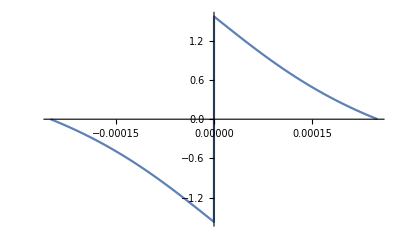

-Graphics-